Paul Fischer
PHYS 550A
10/20/20
Dr. Papp

Homework 3

Problem 1

a)

-Graphics-

First, we define the wave function to the left and right of the jump in the potential at x = y.

```mathematica
SubMinus[ψ][x_]:=A*Exp[I*k*x]+B*Exp[-I*k*x]
SubPlus[ψ][x_]:=C*Exp[I*k'*x]+D*Exp[-I*k'*x]
```

Then, we store the solutions to the continuity equations for the wave functions and their derivatives for the variables of interest, C(A,B) and D(A,B), as an association.

```mathematica
contY =Solve[SubMinus[ψ][y]-SubPlus[ψ][y]== 0&&SubMinus[ψ]'[y]-SubPlus[ψ]'[y]== 0, {C,D}]//Association;
```

We create the matrix S_y(k',k) by taking the derivatives of C(A,B) and D(A,B) with respect to A and B to find the coefficients of each variable in both expressions.

```mathematica
Subscript[S, y]={{D[contY[C],A],D[contY[C],B]},{D[contY[D],A],D[contY[D],B]}}//Simplify;
```

We can now show that it is possible to express the relation in the given form using the calculated matrix S_y(k',k).

```mathematica
Print[
MatrixForm[{{C},{D}}]," - S_y(k',k) ",MatrixForm[{{A},{B}}]," = ",
MatrixForm[Simplify[{{contY[C]},{contY[D]}}-Subscript[S, y].{{A},{B}}]]
]
```

(C
D) - S_y(k',k) (A
B) = (0
0)

```mathematica
Print["S_y(k',k) = ",MatrixForm[Subscript[S, y]]]
```

S_y(k',k) = ((ⅇ^(ⅈ y (k-k')) (k+k'))/(2 k') | (ⅇ^(-ⅈ y (k+k')) (-k+k'))/(2 k')
(ⅇ^(ⅈ y (k+k')) (-k+k'))/(2 k') | (ⅇ^(-ⅈ y (k-k')) (k+k'))/(2 k'))

b)

-Graphics-

First, we calculate S_y^-1(k',k).

```mathematica
sYInv = Simplify[Inverse[Subscript[S, y]]];
Print["S_y^-1(k',k) = ",MatrixForm[sYInv]]
```

S_y^-1(k',k) = ((ⅇ^(-ⅈ y (k-k')) (k+k'))/(2 k) | (ⅇ^(-ⅈ y (k+k')) (k-k'))/(2 k)
(ⅇ^(ⅈ y (k+k')) (k-k'))/(2 k) | (ⅇ^(ⅈ y (k-k')) (k+k'))/(2 k))

Now, we show that S_y^-1(k',k) = S_y(k,k') .

```mathematica
sYKKPrimeSwap = Subscript[S, y]/.{k->k',k'->k};
Print["S_y^-1(k',k) - S_y(k,k') = ",MatrixForm[Simplify[sYInv-sYKKPrimeSwap]]]
```

S_y^-1(k',k) - S_y(k,k') = (0 | 0
0 | 0)

c)

-Graphics-

First, we define the wave function surrounding the discontinuity points, x ∈ {0, a}, of the potentials with reflection and transmission amplitudes ℜ and 𝔗, where Ε = e^-ika 𝔗 (Note, I am using Ε (Capital Epsilon) instead of E so that the compiler doesn’t confuse the letter E with Euler’s number).

```mathematica
Subscript[ψ, x<0][x_]:=Exp[I*k*x]+ℜ*Exp[-I*k*x]
Subscript[ψ, 0<x<a][x_]:=C*Exp[-κ'*x]+D*Exp[κ'*x]
Subscript[ψ, x>a][x_]:=Ε*Exp[I*k*x]
```

We store the solutions to the continuity equations for the wave functions and their derivatives at each discontinuity point for the variables of interest, {C(ℜ), D(ℜ), C(Ε), D(Ε)}, as associations.

```mathematica
cont0 =Solve[Subscript[ψ, x<0][0]-Subscript[ψ, 0<x<a][0]== 0&&Subscript[ψ, x<0]'[0]-Subscript[ψ, 0<x<a]'[0]== 0, {C,D}]//Association;
contA =Solve[Subscript[ψ, 0<x<a][a]-Subscript[ψ, x>a][a]== 0&&Subscript[ψ, 0<x<a]'[a]-Subscript[ψ, x>a]'[a]== 0, {C,D}]//Association;
```

Then, we create the matrices S_0(κ',k) and S_a(κ',k) such that they satisfy the following relations* by taking derivatives to find the coefficients for the variables of interest (or subtracting the multiple of the variable with its respective derivative from the solution for terms without a variable of interest).

```mathematica
Subscript[S, 0]={
{cont0[C]-ℜ*D[cont0[C],ℜ],D[cont0[C],ℜ]},{cont0[D]-ℜ*D[cont0[D],ℜ],D[cont0[D],ℜ]}
}//Simplify;
Subscript[S, a]={
{contA[C]-Ε*D[contA[C],Ε],D[contA[C],Ε]},{contA[D]-Ε*D[contA[D],Ε],D[contA[D],Ε]}
}//Simplify;
Style["*",Bold,Large]
Print[
MatrixForm[{{C},{D}}]," - S_0(κ',k) ",MatrixForm[{{1},{ℜ}}]," = ",
MatrixForm[Simplify[{{cont0[C]},{cont0[D]}}-Subscript[S, 0].{{1},{ℜ}}]]
]
Print[
MatrixForm[{{C},{D}}]," - S_a(κ',k) ",MatrixForm[{{1},{Ε}}]," = ",
MatrixForm[Simplify[{{contA[C]},{contA[D]}}-Subscript[S, a].{{1},{Ε}}]]
]
```

*

(C
D) - S_0(κ',k) (1
ℜ) = (0
0)

(C
D) - S_a(κ',k) (1
Ε) = (0
0)

We can now print the boundary conditions at the discontinuity points of the potentials in terms of the S matrices that satisfy the above relations*.

```mathematica
Print["S_0(κ',k) = ",MatrixForm[Subscript[S, 0]]]
Print["S_a(κ',k) = ",MatrixForm[Subscript[S, a]]]
```

S_0(κ',k) = (1/2-(ⅈ k)/(2 κ') | 1/2+(ⅈ k)/(2 κ')
1/2+(ⅈ k)/(2 κ') | 1/2-(ⅈ k)/(2 κ'))

S_a(κ',k) = (0 | (ⅇ^(a (ⅈ k+κ')) (-ⅈ k+κ'))/(2 κ')
0 | (ⅇ^(ⅈ a k-a κ') (ⅈ k+κ'))/(2 κ'))

We can also rearrange the above relations* to express ℜ(Ε).

```mathematica
Print[
MatrixForm[{{1},{ℜ}}]," - S_0(κ',k)^-1S_a(κ',k) ",MatrixForm[{{1},{Ε}}]," = ",
MatrixForm[
Simplify[
Inverse[Subscript[S, 0]].{{contA[C]},{contA[D]}}-Inverse[Subscript[S, 0]].Subscript[S, a].{{1},{Ε}}
]
]
]
Print["S_0(κ',k)^-1S_a(κ',k) = ",MatrixForm[Inverse[Subscript[S, 0]].Subscript[S, a]]]
```

(1
ℜ) - S_0(κ',k)^-1S_a(κ',k) (1
Ε) = (0
0)

S_0(κ',k)^-1S_a(κ',k) = (0 | (ⅈ ⅇ^(a (ⅈ k+κ')) (1/2-(ⅈ k)/(2 κ')) (-ⅈ k+κ'))/(2 k)+(ⅈ ⅇ^(ⅈ a k-a κ') (-1/2-(ⅈ k)/(2 κ')) (ⅈ k+κ'))/(2 k)
0 | (ⅈ ⅇ^(a (ⅈ k+κ')) (-1/2-(ⅈ k)/(2 κ')) (-ⅈ k+κ'))/(2 k)+(ⅈ ⅇ^(ⅈ a k-a κ') (1/2-(ⅈ k)/(2 κ')) (ⅈ k+κ'))/(2 k))

d)

-Graphics-

In the previous step, we created S matrices that represented C and D as functions of ℜ ( S_0(κ',k) ) and Ε ( S_a(κ',k) ).  We can now set these expressions equal to each other to solve for the reflection amplitude ℜ and transmission amplitude 𝔗 (remembering that Ε = e^-ika 𝔗).

```mathematica
rTAmp=Solve[Subscript[S, a].{{1},{Ε}}-Subscript[S, 0].{{1},{ℜ}}==0,{ℜ,Ε}]//Association;
```

```mathematica
ℜAmp = rTAmp[ℜ]//Simplify;
𝔗Amp=rTAmp[Ε]*Exp[I*k*a]//Simplify;
Print["ℜ = ",ℜAmp]
Print["𝔗 = ",𝔗Amp]
```

ℜ = -((-1+ⅇ^(2 a κ')) (k-ⅈ κ') (k+ⅈ κ'))/(-(-1+ⅇ^(2 a κ')) k^2-2 ⅈ (1+ⅇ^(2 a κ')) k κ'+(-1+ⅇ^(2 a κ')) (κ')^2)

𝔗 = (4 ⅈ ⅇ^(a κ') k κ')/((-1+ⅇ^(2 a κ')) k^2+2 ⅈ (1+ⅇ^(2 a κ')) k κ'-(-1+ⅇ^(2 a κ')) (κ')^2)

We can check that our transmission and reflection amplitudes make physical sense by checking that |ℜ|^2 + |𝔗|^2 = 1.

```mathematica
𝔗AmpTemp = 𝔗Amp/.{a->Re[a],k->Re[k],κ'->I*Re[k']};
ℜAmpTemp = ℜAmp/.{a->Re[a],k->Re[k],κ'->I*Re[k']};
Print[
"|ℜ|^2 + |𝔗|^2 = ",Conjugate[ℜAmpTemp]*ℜAmpTemp+Conjugate[𝔗AmpTemp]*𝔗AmpTemp//Simplify
]
```

|ℜ|^2 + |𝔗|^2 = 1

Problem 2

-Graphics-

First, we can notice that for {x | x > 0}, the potential V(x) is identical to that of the one dimensional harmonic oscillator.  We can also notice that the wave function must vanish for {x | x < 0} due to the infinitely high potential.  Therefore, only the odd solutions of the one dimensional harmonic oscillator will be continuous at the discontinuity point of the potentials {x | x = 0}.  Since our wavefunction is only nontrivial for {x | x > 0}, we must double the one dimensional harmonic oscillator’s amplitude to renormalize it.  This leaves us with the following eigenstates for the system, where H_n(z) = (-1)^n e^(z^2)d^n/dz^n(e^(-z^2)) are the Hermite polynomials:

ψ_n(x) = 2/(√(2^n n!)) · (mω/πℏ)^(1/4)·e^(-mωx^2/(2ℏ))·H_n(√(mω/ℏ)x), n = 1, 3, 5, ...

The corresponding eigenvalues to these eigenstates are as follows:

E_n= ℏω(n+1/2), n = 1, 3, 5, ...

Problem 3

-Graphics-

First, we define the given potential energy, kinetic energy, and total energy operators as functions using the lower limit of the Heisenberg uncertainty relation ΔxΔp≥ℏ/2.

```mathematica
V[x_]:=(m*ω^2*x^2)/2+λ'*x^4
T[p_]:=p^2/(2*m)
Ε[Δx_]:=T[ℏ/(2*Δx)]+V[Δx]
```

We can draw the potential curve V(x) for x ∈ [0, 1] in natural units, where m = ω = λ' = 1.

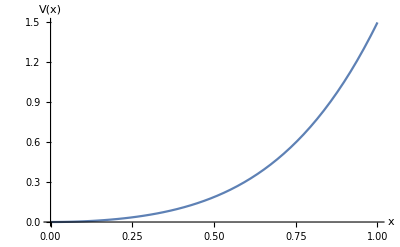

```mathematica
Plot[x^2/2+x^4,{x,0,1},AxesLabel->{"x","V(x)"}]
```

We can start solving for the ground state energy by minimizing the total energy function with respect to Δx.  This yields a 6^th degree polynomial solution, providing 6 different possible ground state energies.  We can look at one of the solutions below in natural units to observe something interesting, the energy eigenstate with ω^2<0 is less than the eigenstate with ω^2>0.  This means that this possible ground state energy is at a minimum when the frequency is complex.

```mathematica
solnsDeltaX=Solve[D[Ε[Δx],Δx]==0,Δx]//Simplify;
deltaXArray=solnsDeltaX[[All,1,2]];
Print["Ε_ground(Δx_1) = ",Ε[deltaXArray[[1]]]]
omegaReal=Ε[deltaXArray[[1]]]/.{ℏ-> 1,λ'-> 1,m-> 1,ω-> 1}//Simplify;
omegaComplex=Ε[deltaXArray[[1]]]/.{ℏ-> 1,λ'-> 1,m-> 1,ω-> I}//Simplify;
omegaCfArray={omegaReal,omegaComplex};
minIndex=Position[omegaCfArray,Min[omegaCfArray]][[1,1]];
If[minIndex==1,
Print["Ε_ground(ω^2 > 0) < Ε_ground(ω^2 < 0)"],
Print["Ε_ground(ω^2 < 0) < Ε_ground(ω^2 > 0)"]
]
```

Ε_ground(Δx_1) = (3 ℏ^2 λ')/(2 (-m^2 ω^2+(m^4 ω^4)/((-m^6 ω^6+54 m^2 ℏ^2 (λ')^2+6 √(-3 m^8 ω^6 ℏ^2 (λ')^2+81 m^4 ℏ^4 (λ')^4))^(1/3))+(-m^6 ω^6+54 m^2 ℏ^2 (λ')^2+6 √(-3 m^8 ω^6 ℏ^2 (λ')^2+81 m^4 ℏ^4 (λ')^4))^(1/3)))+1/(24 λ')ω^2 (-m^2 ω^2+(m^4 ω^4)/((-m^6 ω^6+54 m^2 ℏ^2 (λ')^2+6 √(-3 m^8 ω^6 ℏ^2 (λ')^2+81 m^4 ℏ^4 (λ')^4))^(1/3))+(-m^6 ω^6+54 m^2 ℏ^2 (λ')^2+6 √(-3 m^8 ω^6 ℏ^2 (λ')^2+81 m^4 ℏ^4 (λ')^4))^(1/3))+1/(144 m^2 λ')(-m^2 ω^2+(m^4 ω^4)/((-m^6 ω^6+54 m^2 ℏ^2 (λ')^2+6 √(-3 m^8 ω^6 ℏ^2 (λ')^2+81 m^4 ℏ^4 (λ')^4))^(1/3))+(-m^6 ω^6+54 m^2 ℏ^2 (λ')^2+6 √(-3 m^8 ω^6 ℏ^2 (λ')^2+81 m^4 ℏ^4 (λ')^4))^(1/3))^2

Ε_ground(ω^2 < 0) < Ε_ground(ω^2 > 0)

We can find further bound the lower limit of the ground state by finding the lower limit of the expectation value of the Hamiltonian and minimizing it with respect to ⟨x^2⟩.

⟨Ĥ⟩ ≥ ℏ^2/(8⟨x^2⟩) + mω/2⟨x^2⟩ + λ'⟨x^2⟩^2
(d⟨Ĥ⟩)/(d⟨x^2⟩) = -ℏ^2/(8⟨x^2⟩^2)+mω/2+2 λ'⟨x^2⟩ = 0

This reveals the following cubic equation which we can solve for ⟨x^2⟩.

⟨x^2⟩^3 + mω/(4 λ')⟨x^2⟩^2 - ℏ^2/(16 λ') = 0

```mathematica
soln=Solve[x^3+(m*ω)/(4*λ')*x^2-ℏ^2/(16*λ')==0,x]//FullSimplify
```

{{x→1/12 (((-m^3 ω^3+6 λ' (9 ℏ^2 λ'+√(-3 m^3 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3)+(m ω (-1+(m ω)/(λ' ((-m^3 ω^3+6 λ' (9 ℏ^2 λ'+√(-3 m^3 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))))/λ')},{x→1/24 (-(2 m ω)/λ'+((-1-ⅈ √3) m^2 ω^2)/((λ')^2 ((-m^3 ω^3+6 λ' (9 ℏ^2 λ'+√(-3 m^3 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+ⅈ (ⅈ+√3) ((-m^3 ω^3+6 λ' (9 ℏ^2 λ'+√(-3 m^3 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))},{x→1/24 (-(2 m ω)/λ'+(ⅈ (ⅈ+√3) m^2 ω^2)/((λ')^2 ((-m^3 ω^3+6 λ' (9 ℏ^2 λ'+√(-3 m^3 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+(-1-ⅈ √3) ((-m^3 ω^3+6 λ' (9 ℏ^2 λ'+√(-3 m^3 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))}}

We can plug the square root of the real value for ⟨x^2⟩ into the Hamiltonian to solve for the ground state energy.  In natural units, with appropriately large λ', a real energy can be returned with a real frequency, but a complex energy is returned for a complex frequency (albeit with a lesser real part).  Both complex and real frequencies return complex energies for the other solutions of the cubic equation.

```mathematica
Print["Ε_ground = ",Ε[Sqrt[1/12 (-(7 ω)/λ'+(49 ω^2)/((λ')^2 ((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))]]]
```

Ε_ground = (3 ℏ^2)/(2 m (-(7 ω)/λ'+(49 ω^2)/((λ')^2 ((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3)))+1/24 m ω^2 (-(7 ω)/λ'+(49 ω^2)/((λ')^2 ((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+1/144 λ' (-(7 ω)/λ'+(49 ω^2)/((λ')^2 ((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))^2

```mathematica
Ε[Sqrt[1/12 (-(7 ω)/λ'+(49 ω^2)/((λ')^2 ((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))]]/.{ℏ-> 1,λ'-> 4,m-> 1,ω-> 1}//N
```

0.959049

```mathematica
Ε[Sqrt[1/12 (-(7 ω)/λ'+(49 ω^2)/((λ')^2 ((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))+((-343 ω^3+6 λ' (9 ℏ^2 λ'+√(-1029 ω^3 ℏ^2+81 ℏ^4 (λ')^2)))/(λ')^3)^(1/3))]]/.{ℏ-> 1,λ'-> 4,m-> 1,ω-> I}//N
```

0.514567+0.221916 ⅈ

Problem 4

a)

-Graphics-

First, we can prove [â , â^(†^m)] = m â^(†^(m-1)) by induction.

The ladder operators operate on the energy eigenstates of the harmonic oscillator as follows:
â^†|n⟩ = √(n+1) |n + 1⟩
â |n⟩ = √n |n - 1⟩.

We can first prove the desired relationship in the m = 1 case.

[â , â^†] |n⟩ =  â â^†|n⟩ - â^†â |n⟩ 
                      = √(n+1)â |n + 1⟩ - √nâ^†|n - 1⟩
                      = (n + 1) |n⟩ - n |n⟩
                      = |n⟩
∴    [â , â^†] = 1

Now, we assume the relationship holds in the m = k case, [â , â^(†^k)] = k â^(†^(k-1)), and show that it holds in the m = k + 1 case.

[â , â^(†^(k+1))] |n⟩ =  â â^(†^(k+1))|n⟩ - â^(†^(k+1))â |n⟩ 
                           = (√(n+1)√(n+2)...√(n+k+1))â |n + k + 1⟩ - â^(†^(k+1))√n |n - 1⟩
                           = (√(n+1)√(n+2)...√(n+k))(n + k + 1) |n + k⟩ - (n √(n+1)√(n+2)...√(n+k))|n + k⟩
                           = (k + 1) (√(n+1)√(n+2)...√(n+k)) |n + k⟩
                           = (k + 1) (√(n+1)√(n+2)...√(n+k)) (â^(†^k))/(√(n+1)√(n+2)...√(n+k)) |n⟩
                           = (k + 1) â^(†^k)|n⟩
 ∴   [â , â^(†^(k+1))] = (k + 1) â^(†^k) ◼

We can check this relation programmatically.  We start by defining the respective lowering and raising operators acting on a state n, 
â |n⟩ and â^†|n⟩, as well as a function that finds the commutator between a and the m^th power of â^†, [a, â^(†^m)].

```mathematica
â[{coeff_,n_}]:={coeff*Sqrt[n],n-1}
SuperDagger[â][{coeff_,n_}]:={coeff*Sqrt[n+1],n+1}
commAADagMthPwr[â_,âDag_,m_]:=
Simplify[
{
â[Nest[âDag,{1,n},m]][[1]]-Nest[âDag,â[{1,n}],m][[1]],
â[Nest[âDag,{1,n},m]][[2]]
}
]
```

We can define a function that prints a formatted output of the previously defined commutator function.

```mathematica
commPrint[comm_]:=
Module[
{i=0,res1=comm[[2]]-n,j=1,res2=1},
While[
res1>0,
res1=res1-1;
i++;
];
While[
j<i+1,
res2=res2/(√(n+j));
j++;
];
Print["[â , â^†"^j, "] = ",comm[[1]]*res2*"â^†"^i,"\n"]
]
```

We can see that the relationship holds for {m | m ∈ ℕ ≤ 6}.

```mathematica
For[m=1,m≤6,m++,
commPrint[commAADagMthPwr[â,SuperDagger[â],m]]
]
```

[â , â^†] = 1

([â , â^†)^2] = 2 â^†

([â , â^†)^3] = 3 (â^†)^2

([â , â^†)^4] = 4 (â^†)^3

([â , â^†)^5] = 5 (â^†)^4

([â , â^†)^6] = 6 (â^†)^5

Using the properties [A, B] = -[B, A], (A (B))^† = B^†A^† and (A^†)^†=A, we can see that [â^†, â^m] = -[â^m, â^†] = -[â , â^(†^m)]^† = -(m â^(†^(m-1)))^† = -m â^(^(m-1)).

Using these relations, [â , â^(†^m)] = m â^(†^(m-1)) and [â^†, â^m] = -m â^(^(m-1)), we can now calculate the commutators [â , f(â^†)] and [â^† , f(â)] for f being a power, a polynomial, and a convergent power series.  For f being a polynomial, we programmatically solve for the partial sum formula in the following form (and likewise with the other relation with respect to â):
[â , â^† + â^(†^2) + ... + â^(†^m)] =  1 + 2 â^† + ... + m â^(†^(m-1))
                      [â , ∑_(l=1)^m â^(†^l)] =  ∑_(l=1)^m l â^(†^(l-1))

```mathematica
∑_(l=1)^m l*SuperDagger[â]^(l-1)//Simplify
∑_(l=1)^m -l*â^(l-1)//Simplify
```

1+2 â^†+3 (â^†)^2+4 (â^†)^3+5 (â^†)^4+6 (â^†)^5+7 (â^†)^6

-1-2 â-3 â^2-4 â^3-5 â^4-6 â^5-7 â^6

For the convergent power series, we can notice that [â , ∑_(m=1)^∞ â^(†^m)] = ∑_(m=1)^∞ m â^(†^(m-1)) gives the derivative of the infinite geometric sequence with respect to â^†(and likewise with the other relation with respect to â).

```mathematica
∑_(m=1)^∞ m*SuperDagger[â]^(m-1)
∑_(m=1)^∞ -m*â^(m-1)
```

1/((-1+â^†)^2)

-1/(-1+â)^2

We can now express the commutators, [â , f(â^†)] and [â^† , f(â)], for f being a power, a polynomial, and a convergent power series.

power: [â , â^(†^m)] = m â^(†^(m-1)), [â^†, â^m] = -m â^(^(m-1))
polynomial: [â , ∑_(l=1)^m â^(†^l)]  = (1-(1+m) (â^†)^m+m (â^†)^(1+m))/((-1+â^†)^2), [â^† , ∑_(l=1)^m â^(^l)]  = (-1-â^(1+m) m+â^m (1+m))/(-1+â)^2
convergent power series: [â , ∑_(m=1)^∞ â^(†^m)] = 1/((-1+â^†)^2) ,  [â^† , ∑_(m=1)^∞ â^(^m)] = -1/(-1+â)^2

b)

-Graphics-

Using the commutation relation, we can re-write the left hand side of the first equation.

â f(â^†) |0⟩ = [â , f(â^†)] |0⟩ + f(â^†) â |0⟩

The second term in the sum vanishes since the |0⟩ state cannot be lowered.

â f(â^†) |0⟩ = [â , f(â^†)] |0⟩

For the f being a power case,

â f(â^†) |0⟩ = [â , f(â^†)] |0⟩
                     = m â^(†^(m-1)) |0⟩
                     = d/dâ^†(â^†)^m |0⟩
                     = f'(â^†) |0⟩.

Since the derivative is a linear operator, the f being a polynomial and f being a convergent power series cases will yield the same result since they are both linear combinations of the f being a power case.

We have just shown that operating on a function (power, polynomial, or convergent power series) of â^† operating on the 0 state with the lowering operator â yields the derivative of that function with respect to â^†operating on the 0 state.  Since the derivative of all of these functions does not change its type (i.e. the derivative of a polynomial is still a polynomial), the same rule should apply to the derivatives of the function.

â^2 f(â^†) |0⟩ = â (â f(â^†)) |0⟩
                       = â (f'(â^†)) |0⟩
                       = f''(â^†) |0⟩

c)

-Graphics-

First, we show that the even and odd states can be expressed as convergent power series f(â^†) |0⟩ by calculating their MacLaurin series.

```mathematica
Print["|η,+⟩ = (",Series[1/(√Cosh[Abs[η]^2])*Cosh[η*SuperDagger[â]], {SuperDagger[â],0,5}],") |0⟩"]
Print["|η,-⟩ = (",Series[1/(√Sinh[Abs[η]^2])*Sinh[η*SuperDagger[â]], {SuperDagger[â],0,5}],") |0⟩"]
```

|η,+⟩ = (1/(√Cosh[Abs[η]^2])+(η^2 (â^†)^2)/(2 √Cosh[Abs[η]^2])+(η^4 (â^†)^4)/(24 √Cosh[Abs[η]^2])+O[â^†]^6) |0⟩

|η,-⟩ = ((η â^†)/(√Sinh[Abs[η]^2])+(η^3 (â^†)^3)/(6 √Sinh[Abs[η]^2])+(η^5 (â^†)^5)/(120 √Sinh[Abs[η]^2])+O[â^†]^6) |0⟩

Now that we have shown that the even and odd states can be constructed as convergent power series f(â^†)|0⟩, we can use the previous result to calculate [â^2, f(â^†)] |0⟩ for both operators.

[â^2, f(â^†)] |0⟩ = â^2f(â^†) |0⟩ - f(â^†) â^2|0⟩
                           = f''(â^†) |0⟩

We can show that f''(â^†) |0⟩ can be expressed in terms of f(â^†) |0⟩ by creating the functions f(â^†) ∈ {η^+, η^-} and dividing their second derivatives by themselves.

```mathematica
SuperPlus[η]=1/(√Cosh[Abs[η]^2])*Cosh[η*SuperDagger[â]];
SuperMinus[η]=1/(√Sinh[Abs[η]^2])*Sinh[η*SuperDagger[â]];
Print["TraditionalForm` = ",D[SuperPlus[η],{SuperDagger[â],2}]/SuperPlus[η],"TraditionalForm`"]
Print["TraditionalForm` = ",D[SuperMinus[η],{SuperDagger[â],2}]/SuperMinus[η],"TraditionalForm`"]
```

TraditionalForm` = η^2 TraditionalForm`

TraditionalForm` = η^2 TraditionalForm`

Therefore, for both the even and odd states,

[â^2, f(â^†)] |0⟩ = η^2f(â^†)|0⟩,

which proves that the even and odd states are eigenstates of â^2.

Problem 5

a)

-Graphics-

First let’s remember what we knew about the harmonic oscillator.  Since [â , â^†] = 1 and N̂ = â^†â, we can define the following:

â^†|n⟩ = √(n+1) |n + 1⟩
â |n⟩ = √n |n - 1⟩
N̂ |n⟩ = n |n⟩

Using these properties, and f(Â) = ∑_i f(α_i) |ϕ_i⟩⟨ϕ_i|, let us observe what happens to the eigenstates n under the action of these operators.

(Ĵ)_+ |n⟩ = √(2j - N̂)â |n⟩
             = √(n(2j - OverHat[N)]) |n - 1⟩
             = √(n(2j - (n-1) )) |n - 1⟩
             = √(n^2 - n(2j-1)) |n - 1⟩

(Ĵ)_- |n⟩ = â^†√(2j - N̂) |n⟩
             = √(2j - n)â^† |n⟩
             = √((n+1)(2j - n)) |n + 1⟩
             = √(-n^2 + (2j - 1) n + 2j)|n + 1⟩

We can see that both operators take us to another state within the subspace.

Let us first observe what happens when (Ĵ)_+ acts on the 0 state, remembering thatâ |0⟩ = 0 .

(Ĵ)_+ |0⟩ = √(2j - N̂)â |0⟩
             = 0

Now, let us observe what happens when (Ĵ)_- acts on the 2j state.

(Ĵ)_- |2j⟩ = (â)^†√(2j - N̂) |2j⟩
             = (â)^†√(2j - 2j) |2j⟩
             = 0

Now we can see that the operators can take us to other states in the subspace, but can’t take us out of the subspace.  Therefore, both operators act on the subspace spanned by the eigenstates of Ĥ, |0⟩, |1⟩, |2⟩, ..., |2j⟩, and their action leaves the subspace invariant.

b)

-Graphics-

First, we can solve for each quantity of the first commutator and find the relationship.

(Ĵ)_+(Ĵ)_- = ((Ĵ)_1 + i(Ĵ)_2)((Ĵ)_1 - i(Ĵ)_2)
            = ((Ĵ)_1)^2 + ((Ĵ)_2)^2 + i((Ĵ)_2(Ĵ)_1 - (Ĵ)_1(Ĵ)_2)

(Ĵ)_-(Ĵ)_+ = ((Ĵ)_1 - i(Ĵ)_2)((Ĵ)_1 + i(Ĵ)_2)
            = ((Ĵ)_1)^2 + ((Ĵ)_2)^2 - i((Ĵ)_2(Ĵ)_1 - (Ĵ)_1(Ĵ)_2)

[(Ĵ)_+, (Ĵ)_-] = (Ĵ)_+(Ĵ)_- - (Ĵ)_-(Ĵ)_+
                 = 2i((Ĵ)_2(Ĵ)_1 - (Ĵ)_1(Ĵ)_2)

∴ (Ĵ)_3 = i((Ĵ)_2(Ĵ)_1 - (Ĵ)_1(Ĵ)_2)
          = i[(Ĵ)_2, (Ĵ)_1]

We can see the pattern [(Ĵ)_j, (Ĵ)_k] = iϵ_jkl(Ĵ)_l, and use this to prove that this (Ĵ)_3 we calculated satisfies the second relation.

[(Ĵ)_3, (Ĵ)_+] = (Ĵ)_3((Ĵ)_1 + i(Ĵ)_2) - ((Ĵ)_1 + i(Ĵ)_2)(Ĵ)_3
                 = ((Ĵ)_3(Ĵ)_1 - (Ĵ)_1(Ĵ)_3) - i((Ĵ)_2(Ĵ)_3 - (Ĵ)_3(Ĵ)_2)
                 = i(Ĵ)_2 - i(i(Ĵ)_1)
                 = (Ĵ)_1 + i(Ĵ)_2
                 = (Ĵ)_+

[(Ĵ)_3, (Ĵ)_-] = (Ĵ)_3((Ĵ)_1 - i(Ĵ)_2) - ((Ĵ)_1 - i(Ĵ)_2)(Ĵ)_3
                 = ((Ĵ)_3(Ĵ)_1 - (Ĵ)_1(Ĵ)_3) - i((Ĵ)_3(Ĵ)_2 - (Ĵ)_2(Ĵ)_3)
                 = i(Ĵ)_2 - i(-i(Ĵ)_1)
                 = -(Ĵ)_1 + i(Ĵ)_2
                 = -(Ĵ)_-

∴ [(Ĵ)_3, (Ĵ)_±] = ±(Ĵ)_±

c)

-Graphics-

First, we can find expressions for  (Ĵ)_+(Ĵ)_- and (Ĵ)_-(Ĵ)_+ in terms of (Ĵ)^2and (Ĵ)_3.   We want these relationships so that we can find the eigenvalues of (Ĵ)^2and (Ĵ)_3 (our intermediate variable) in terms of raising and lowering operators which have known boundary conditions.  This can be found by rearranging one of the steps from the solution of [(Ĵ)_+, (Ĵ)_-] in part b.

(Ĵ)_+(Ĵ)_- = ((Ĵ)_1 + i(Ĵ)_2)((Ĵ)_1 - i(Ĵ)_2)
            = ((Ĵ)_1)^2 + ((Ĵ)_2)^2 + i((Ĵ)_2(Ĵ)_1 - (Ĵ)_1(Ĵ)_2)
            = (Ĵ)^2 - ((Ĵ)_3)^2- (Ĵ)_3

(Ĵ)_-(Ĵ)_+ = ((Ĵ)_1 - i(Ĵ)_2)((Ĵ)_1 + i(Ĵ)_2)
            = ((Ĵ)_1)^2 + ((Ĵ)_2)^2 - i((Ĵ)_2(Ĵ)_1 - (Ĵ)_1(Ĵ)_2)
            = (Ĵ)^2 - ((Ĵ)_3)^2+ (Ĵ)_3

We can show that (Ĵ)_3 commutes with (Ĵ)^2by using the relation [(Ĵ)_j, (Ĵ)_k] = iϵ_jkl(Ĵ)_l proven in part b.

[(Ĵ)_3, (Ĵ)^2] = [(Ĵ)_3, ((Ĵ)_1)^2 + ((Ĵ)_2)^2 + ((Ĵ)_3)^2]
                 = [(Ĵ)_3, ((Ĵ)_1)^2] + [(Ĵ)_3, ((Ĵ)_2)^2]
                 = (Ĵ)_1[(Ĵ)_3, (Ĵ)_1] + [(Ĵ)_3, (Ĵ)_1](Ĵ)_1 + (Ĵ)_2[(Ĵ)_3, (Ĵ)_2] + [(Ĵ)_3, (Ĵ)_2](Ĵ)_2
                 = (Ĵ)_1(i(Ĵ)_2) + (i(Ĵ)_2)(Ĵ)_1 + (Ĵ)_2(-i(Ĵ)_1) + (-i(Ĵ)_1)(Ĵ)_2
                 = i(Ĵ)_1(Ĵ)_2 -  i(Ĵ)_1(Ĵ)_2 + i(Ĵ)_2(Ĵ)_1 -  i(Ĵ)_2(Ĵ)_1
                 = 0

By the symmetry of components, we conclude from this that all operators (Ĵ)_i (i ∈ {1, 2, 3}) commute with  (Ĵ)^2, which means that the operators (Ĵ)_± also commute with (Ĵ)^2.  We use these commutation relations to find the eigenvalues of (Ĵ)^2 and (Ĵ)_3 from their common normalized eigenstates ⟨α’, β’ | α, β⟩ = δ_αα' δ_ββ':

(Ĵ)^2|α, β⟩ = α|α, β⟩ and (Ĵ)_3|α, β⟩ = β|α, β⟩.

Using  [(Ĵ)_±, (Ĵ)^2] = 0,

(Ĵ)^2((Ĵ)_±|α, β⟩) = (Ĵ)_±(Ĵ)^2|α, β⟩
                          = α(Ĵ)_±|α, β⟩.

Using [(Ĵ)^2, (Ĵ)_3] = 0,

(Ĵ)_3((Ĵ)_±|α, β⟩) = ((Ĵ)_±(Ĵ)_3 ± (Ĵ)_3)|α, β⟩
                          = (β ± 1)(Ĵ)_±|α, β⟩.

We can see here that applying the (Ĵ)_± operators changes the eigenstates only by raising or lowering the state β by 1.  Since we proved in part a that (Ĵ)_+ and (Ĵ)_- act on the subspace spanned by the eigenstates of Ĥ and their action leaves the subspace invariant, there have to be lower and upper bounds on β.  We can calculate these bounds as functions of α.

α - β^2 = ⟨α, β |((Ĵ)^2 - ((Ĵ)_3)^2)|α, β⟩ 
             = ⟨α, β |(((Ĵ)_1)^2 + ((Ĵ)_2)^2)|α, β⟩ 
             ≥ 0

We see here that β must be bounded from above and below by α ≥ β^2 ≥ 0.  Let us now solve for the maximum value of β such that (Ĵ)_+|α, β_max⟩ = 0.

0 = (Ĵ)_-(Ĵ)_+|α,  β_max⟩
   = ((Ĵ)^2 - ((Ĵ)_3)^2- (Ĵ)_3)|α,  β_max⟩ 
   = (α - (β^2)_max - β_max)|α,  β_max⟩

We now have α(β_max): α = β_max(β_max + 1).  Let us now calculate the minimum value of β such that (Ĵ)_-|α, β_min⟩ = 0.

0 = (Ĵ)_+(Ĵ)_-|α,  β_min⟩
   = ((Ĵ)^2 - ((Ĵ)_3)^2+ (Ĵ)_3)|α,  β_min⟩ 
   = (α - (β^2)_min + β_min)|α, β_min⟩

This tells is that α must also be {α | α = β_min(β_min - 1)}.  Therefore,  β_max must be {β_max | β_max = -β_min}.  There must be some integer n that represents the number of times the (Ĵ)_+operator must act on β_min to raise it to β_max:

β_max = β_min + n
           = -β_max + n.

∴  β_max = n/2

This tells us that β  can take half integer values.  If we make the substitutions j = β_max and m =β, we can rewrite our equation for α:

α = j(j + 1), where -j ≤ m ≤ j and j = 0, 1/2, 1, 3/2, 2, ...

We can plug this expression into the eigenvalue equation for (Ĵ)^2 and obtain the relation which had to be proven.

(Ĵ)^2|j, m⟩ = j(j + 1)|j, m⟩

∴ (Ĵ)^2 =  j(j + 1)𝕀

Problem 6

a)

-Graphics-
-Graphics-

The general form of the partner potentials V_± in terms of the super potential W(x) is given by

V_± = W^2(x) ∓ W’(x).

We start by defining the partner potentials as functions.

```mathematica
SubPlus[V][W_]:=W^2-D[W,x]
SubMinus[V][W_]:=W^2+D[W,x]
```

We can now create the different functions W(x) and plug them into the functions V_± to calculate the partner potentials for each given super potential.

```mathematica
Subscript[W, a][x_]:=ω*x
Print["V_+ = ", SubPlus[V][Subscript[W, a][x]]]
Print["V_- = ", SubMinus[V][Subscript[W, a][x]]]
```

V_+ = -ω+x^2 ω^2

V_- = ω+x^2 ω^2

b)

-Graphics-

We use the same process described previously to calculate the partner potentials.

```mathematica
Subscript[W, b][x_,λ_]:=λ*Tanh[x]
Print["V_+ = ", SubPlus[V][Subscript[W, b][x,λ]]]
Print["V_- = ", SubMinus[V][Subscript[W, b][x,λ]]]
```

V_+ = -λ Sech[x]^2+λ^2 Tanh[x]^2

V_- = λ Sech[x]^2+λ^2 Tanh[x]^2

We examine the case λ = 1.

```mathematica
Print["V_+(λ = 1) = ", SubPlus[V][Subscript[W, b][x,1]]]
Print["V_-(λ = 1) = ", Simplify[SubMinus[V][Subscript[W, b][x,1]]]]
```

V_+(λ = 1) = -Sech[x]^2+Tanh[x]^2

V_-(λ = 1) = 1

V_+(λ = 1) can be rewritten as 1 - 2 sech^2(x) which for small x resembles the harmonic oscillator.

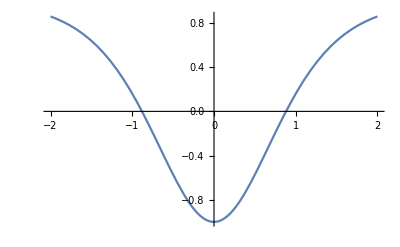

```mathematica
Plot[Tanh[x]^2-Sech[x]^2,{x,-2,2}]
```

V_-(λ = 1) is just a constant value of 1 for all x.

c)

-Graphics-

We use the same process described previously to calculate the partner potentials.

```mathematica
Subscript[W, c][x_,λ_]:=λ*Tan[x]
Print["V_+ = ", SubPlus[V][Subscript[W, c][x,λ]]]
Print["V_- = ", SubMinus[V][Subscript[W, c][x,λ]]]
```

V_+ = -λ Sec[x]^2+λ^2 Tan[x]^2

V_- = λ Sec[x]^2+λ^2 Tan[x]^2

We examine the case λ -> 1.

```mathematica
Print["V_+(λ -> 1) = ", Simplify[SubPlus[V][Subscript[W, c][x,1]]]]
Print["V_-(λ -> 1) = ",SubMinus[V][Subscript[W, c][x,1]]]
```

V_+(λ -> 1) = -1

V_-(λ -> 1) = Sec[x]^2+Tan[x]^2

V_+(λ -> 1) is a constant value of -1 for all x.

V_-(λ -> 1) is discontinuous but resembles the harmonic oscillator for small x.

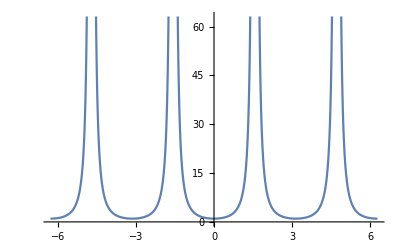

```mathematica
Plot[Tan[x]^2+Sec[x]^2,{x,-2 Pi,2 Pi}]
```

Problem 7

-Graphics-

First, we introduce operators b̂ and (b̂)^† such that when shifted by a constant c,

[â,â^†]/β^2= [β(b̂-c),β((b̂)^†-c)]/β^2 = [b̂, (b̂)^†] = 1.

We insert these operators into the Hamiltonian:

Ĥ = E â â^† + V(â + â^†)
    = E( [â,â^†] + â^†â ) + V(â + â^†)
    = E( [β(b̂-c),β((b̂)^†-c)]  + β((b̂)^†-c)β(b̂-c) ) + V(β(b̂-c)+ β((b̂)^†-c))
    = Eβ^2(1+ (b̂)^†b̂ - c((b̂)^†+ b̂) + c^2) + Vβ((b̂)^†+ b̂ - 2c)
    =  Eβ^2(1+ (b̂)^†b̂ + c^2) + Vβ(- 2c) + ((b̂)^†+ b̂) (Vβ - cEβ^2).

We can calculate the constant shift c such that the ((b̂)^†+ b̂) term is cancelled out.

```mathematica
Solve[V*β-c*Ε*β^2==0, c]
```

{{c→V/(β Ε)}}

The Hamiltonian then becomes:

Ĥ =  Eβ^2(1+ (b̂)^†b̂) - V^2/E.

In the solution of the harmonic oscillator, [b̂, (b̂)^†] = 1 gives us (b̂)^†b̂ = N̂ which has eigenvalues {n | n = 0, 1, 2, ...}.  We can use this to find the eigenvalues of the Hamiltonian.

E_n = Eβ^2(1+ n) - V^2/E, where n = 0, 1, 2, ...

Problem 8

a)

-Graphics-

We can create a visual for the double delta potential V(x) below with a = 1:

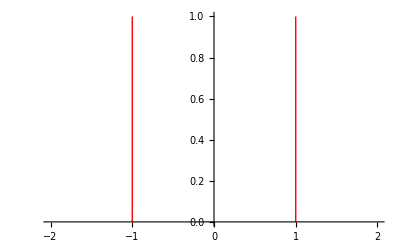

```mathematica
Plot[{100*Sign[x-1],100*Sign[x+1]},{x,-2,2},ExclusionsStyle->Red,PlotRange->{0,1}]
```

We can see that for the double delta potential, V(x) = 0 ∀ x ∉{-a, a}.  The wavefunction can reflect off of or transmit through the points of discontinuity for the potential subject to boundary conditions which we will discuss later.  Since the potential is identically 0 at both sides of either boundary, the wavenumber doesn’t change.  This leaves us with the following wavefunction entering from the left:

ψ(x) = Piecewise[{{e^ikx + ℜe^-ikx, for x < -a}, {Ce^ikx + De^-ikx
Εe^ikx, for -a < x < a 
for x > a.}}]

We define the wavefunction on either side of the points of discontinuity of the potential as functions.

```mathematica
Subscript[ψ, x<-a][x_]:=Exp[I*k*x]+ℜ*Exp[-I*k*x]
Subscript[ψ, -a<x<a][x_]:=C*Exp[I*k*x]+D*Exp[-I*k*x]
Subscript[ψ, x>a][x_]:=𝔗*Exp[I*k*x]
```

The first boundary condition is that the function must be continuous at both boundaries.  We can solve for the functions C(ℜ, 𝔗) and D(ℜ, 𝔗) that satisfy this condition.

```mathematica
contFunc =Solve[Subscript[ψ, x<-a][-a]-Subscript[ψ, -a<x<a][-a]== 0&&Subscript[ψ, -a<x<a][a]-Subscript[ψ, x>a][a]== 0, {C,D}]//Association;
```

Now that we have established that the function is continuous at the boundaries, we have to solve for C(ℜ, 𝔗) and D(ℜ, 𝔗) such that the change in the derivative on both sides of each boundary (bdy) follows:
ψ_left'(bdy)-ψ_right'(bdy)=(-2 mV_0)/ℏ^2 ψ(bdy).

```mathematica
contChgDer=Solve[-Subscript[ψ, x<-a]'[-a]+Subscript[ψ, -a<x<a]'[-a]+(2*m*Subscript[V, 0])/ℏ^2*Subscript[ψ, x<-a][-a]==0&&-Subscript[ψ, x>a]'[a]+Subscript[ψ, -a<x<a]'[a]+(2*m*Subscript[V, 0])/ℏ^2*Subscript[ψ, x>a][a]==0,{C,D}]//Simplify//Association;
```

We can now plug in the functions for C and D from the boundary conditions to solve for the reflection and transmission coefficients, ℜ and 𝔗.

```mathematica
ℜ𝔗Assoc=Solve[contChgDer[C]-contFunc[C]==0&&contChgDer[D]-contFunc[D]==0,{ℜ,𝔗}]//Simplify//Association;
Print["ℜ = ",ℜ𝔗Assoc[ℜ]]
Print["𝔗 = ",ℜ𝔗Assoc[𝔗]]
```

ℜ = -(7 ⅇ^(-2 ⅈ a k) (-1+ⅇ^(4 ⅈ a k)) V_0 (-ⅈ k ℏ^2+7 V_0))/(-k^2 ℏ^4+49 (-1+ⅇ^(4 ⅈ a k)) V_0^2)

𝔗 = (k^2 ℏ^4)/(k^2 ℏ^4-49 (-1+ⅇ^(4 ⅈ a k)) V_0^2)

We can check that our transmission and reflection amplitudes make physical sense by checking that |ℜ|^2 + |𝔗|^2 = 1.

```mathematica
ℜAmpTemp = ℜ𝔗Assoc[ℜ]/.{a->Re[a],k->Re[k],m->Re[m], Subscript[V, 0] ->Re[ Subscript[V, 0] ], ℏ->Re[ ℏ]};
𝔗AmpTemp = ℜ𝔗Assoc[𝔗]/.{a->Re[a],k->Re[k],m->Re[m], Subscript[V, 0] ->Re[ Subscript[V, 0] ], ℏ->Re[ ℏ]};
Print[
"|ℜ|^2 + |𝔗|^2 = ",Conjugate[ℜAmpTemp]*ℜAmpTemp+Conjugate[𝔗AmpTemp]*𝔗AmpTemp//Simplify
]
```

|ℜ|^2 + |𝔗|^2 = 1

b)

-Graphics-

We can calculate the reflected phase shift δ_- using the reflection coefficient we calculated, ℜ = e^(-2 iδ_-), and similarly we can use the transmission coefficient we calculated to solve for the transmitted phase shift δ_+, 𝔗 = e^(-2 iδ_+).

```mathematica
Solve[ℜ𝔗Assoc[ℜ]-Exp[-2*I*SubMinus[δ]]==0,SubMinus[δ]]//Simplify
```

{{δ_-→ConditionalExpression[-π C[1]+1/2 ⅈ Log[-(7 ⅇ^(-2 ⅈ a k) (-1+ⅇ^(4 ⅈ a k)) V_0 (-ⅈ k ℏ^2+7 V_0))/(-k^2 ℏ^4+49 (-1+ⅇ^(4 ⅈ a k)) V_0^2)], C[1]∈ℤ]}}

```mathematica
Solve[ℜ𝔗Assoc[𝔗]-Exp[-2*I*SubPlus[δ]]==0,SubPlus[δ]]//Simplify
```

{{δ_+→ConditionalExpression[-π C[1]+1/2 ⅈ Log[(k^2 ℏ^4)/(k^2 ℏ^4-49 (-1+ⅇ^(4 ⅈ a k)) V_0^2)], C[1]∈ℤ]}}

c)

-Graphics-

The state is bound at the poles of the transmission coefficient; because the wave in that case will asymptotically approach 0 such that it can be normalized.  The transmission coefficient has a pole at the k values satisfying the transcendental (see below) equation k^2 ℏ^4-(-1+ⅇ^(4 ⅈ a k)) m^2 V_0^2=0.

```mathematica
Solve[k^2 ℏ^4-(-1+ⅇ^(4 ⅈ a k)) m^2 Subscript[V, 0]^2==0,k]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[k^2 ℏ^4-49 (-1+ⅇ^(4 ⅈ a k)) V_0^2==0,k]

Problem 9

a)

-Graphics-

First, we define the potential V(x), the wavefunction ψ(x), and the Hamiltonian Ĥ as functions.

```mathematica
V[x_]:=-ℏ^2/m*1/Cosh[x]^2
ψ[x_]:=(Tanh[x]+C)*Exp[I*k*x]
Ĥ[ψ_]:=-ℏ^2/(2m)*D[ψ,{x,2}]+V[x]*ψ
```

We solve the Schrödinger equation for the constant, C(ϵ), as a function of the energy, ϵ, as an association.

```mathematica
cAssoc=Solve[Ĥ[ψ[x]]-ϵ*ψ[x]==0,C]//Simplify//Association
```

<|C→(-2 ⅈ k ℏ^2 Sech[x]^2+(-14 ϵ+k^2 ℏ^2) Tanh[x])/(14 ϵ-k^2 ℏ^2+2 ℏ^2 Sech[x]^2)|>

We can calculate an energy ϵ that will cancel out the tanh(x) terms in the numerator of C(ϵ).

```mathematica
ϵAssoc=Solve[-2 m ϵ+k^2 ℏ^2==0,ϵ]//Association;
Print["ϵ = ",ϵAssoc[ϵ]]
```

ϵ = (k^2 ℏ^2)/14

We can now plug this energy into the expression for C.

```mathematica
Print["C = ",cAssoc[C]/.ϵ->ϵAssoc[ϵ]//Simplify]
```

C = -ⅈ k

To observe the asymptotic behavior, we can plug in our calculated values for C and ϵ and plot their real and imaginary parts for k = 1.

```mathematica
psiLim=ψ[x]/.{C->-I*k,ϵ->(k^2 ℏ^2)/(2 m)};
Print["ψ(x) = ",psiLim]
```

ψ(x) = ⅇ^(ⅈ k x) (-ⅈ k+Tanh[x])

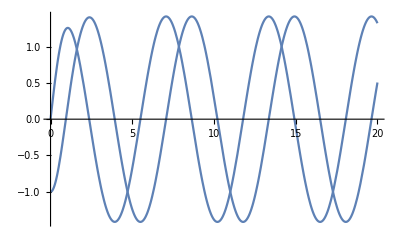

```mathematica
Plot[ReIm[psiLim/.k->1],{x,0,20}]
```

We can see that the function only has a nontrivial ⅇ^(ⅈ k x) component with no ⅇ^(-ⅈ k x)component.  This means that there is no reflection of the wave and only transmission, yielding the following reflection and transmission coefficients:

ℜ = 0
𝔗 = 1.

b)

-Graphics-

First, we can create the function ϕ(x) and solve the Schrödinger equation to find the energy, ϵ.

```mathematica
ϕ[x_]:=Sech[x]
ϵAssocB=Solve[Ĥ[ϕ[x]]-ϵ*ϕ[x]==0,ϵ]//Simplify//Association;
Print["ϵ = ",ϵAssocB[ϵ]]
```

ϵ = -ℏ^2/14

To determine if this state is the ground state or an excited state, let us observe the asymptotic behavior of the function.  We can see from the limit and plot below that the function asymptotically approaches 0 without any nodes.  Since there are no nodes, this is the ground state.

```mathematica
Limit[ϕ[x],x->Infinity]
```

0

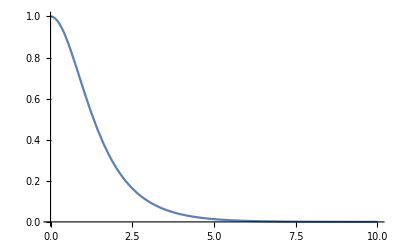

```mathematica
Plot[ϕ[x],{x,0,10}]
```

```mathematica
Print["ϵ_ground = ",ϵAssocB[ϵ]]
```

ϵ_ground = -ℏ^2/14